```mathematica
G := 6.67*10^-8
Mstar := 1.4 * (2*10^33)
rstar := 10^6
gz = G * Mstar/rstar^2
me := 9.109 * 10 ^ -28
mp := 1.672*10^-24
c:=3*10^10
mu := 2
h:=6.626*10^-27
k := 1/(me*c)  * (3*h^3/(8*Pi*mu*mp))^(1/3)
c1:= Pi/3*me^4*c^5/h^3 * 8/5
xf[r_]:= k * r ^ (1/3)
p[r_]= c1* xf[r]^5/Sqrt[1+16/25*xf[r]^2]
```

1.8676×10^14

(3.12516×10^12 r^(5/3))/(√(1+0.0000407921 r^(2/3)))

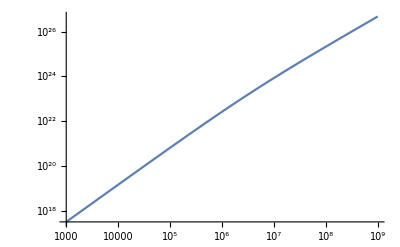

```mathematica
LogLogPlot[p[r],{r,10^3, 10^9}]
```

```mathematica
a[r_] = D[p[r],r]
```

(5.2086×10^12 r^(2/3))/(√(1+0.0000407921 r^(2/3)))-(4.24939×10^7 r^(4/3))/((1+0.0000407921 r^(2/3))^(3/2))

```mathematica
rhoc := 10^9

 sol = NDSolve[{a[rho[z]] * 1/rho[z] * rho'[z] == -gz, rho[0]==rhoc},rho[z],{z, 0, 9313}]
```

{{rho[z]→InterpolatingFunction[…][z]}}

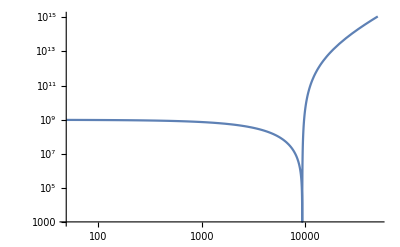

```mathematica
LogLogPlot[Evaluate[rho[z]/.sol], {z, 0, 50000},PlotRange->All]
```

```mathematica
Integrate[Evaluate[rho[z]/.sol],{z,10,15}]
```

{4.98202×10^9}

```mathematica
data = Table[{z,rho[z]/.sol},{z,0,9313, 1}]
Export["Pacsincy.csv",data,"CSV"]
```

{{0,{1.×10^9}},{1,{9.99712×10^8}},{2,{9.99424×10^8}},{3,{9.99136×10^8}},{4,{9.98848×10^8}},9305,{9310,{788.375}},{9311,{480.96}},{9312,{229.168}},{9313,{49.7525}}}
 |  |  |  |

Pacsincy.csv

```mathematica
Directory[]
```

/Users/cristozilleruelo

```mathematica
Clear[rho2]
p2[r_] := 3.12*10^12 * r ^(5/3)
a2[r_] :=  D[p2[r],r]
DSolve[{a2[rho2[z]] * 1/rho2[z]*rho2'[z]==-gz, rho2[0]==10^9}, rho2[z], z]
Clear[rho22]
```

{{rho2[z]→117.161 (41764.8-1. z)^(3/2)}}

117.161 (41764.8-1. z)^(3/2)

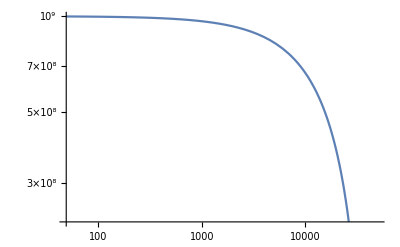

{{z→41764.8}}

```mathematica
rho2[z] = 117.16122229579658 (41764.83186977941-1. z)^(3/2)
LogLogPlot[rho2[z], {z, 0, 50000}]
Solve[rho2[z]==0, z]
```

```mathematica
Clear[rho2]
rhochange = 4037017.258596558
Solve[rho3[z]==rhochange, z]
DSolve[{a2[rho2[z]] * 1/rho2[z] * rho2'[z] == -gz, rho2[8805.6836882763]==rhochange},rho2[z],z]
```

4.03702×10^6

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→rho3^(-1)[4.03702×10^6]}}

{{rho2[z]→117.161 (9864.57-1. z)^(3/2)}}

```mathematica
rho2[z_]=117.16122229579658 (9864.57440646902-1. z)^(3/2)
```

117.161 (9864.57-1. z)^(3/2)

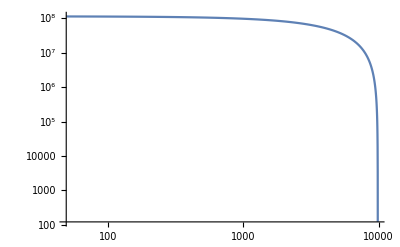

```mathematica
LogLogPlot[rho2[z],{z,0,50000}, PlotRange->All]
```

```mathematica
p3[r_] = 4.89*10^14 * r ^(4/3)
a3[r_] =  D[p3[r],r]
```

4.89×10^14 r^(4/3)

6.52×10^14 r^(1/3)

```mathematica
zchange = 40705.9
Clear[rho3]
DSolve[{a3[rho3[z]] * 1/rho3[z] * rho3'[z] == -gz, rho3[0]==10^9},rho3[z],z]
```

40705.9

{{rho3[z]→-0.000870452 (-1.14883×10^12+3.29072×10^8 z-31420. z^2+1. z^3)},{rho3[z]→-0.000870452 ((-1.14883×10^12-0.000162312 ⅈ)-(1.64536×10^8+2.84985×10^8 ⅈ) z+(15710.-27210.5 ⅈ) z^2+1. z^3)},{rho3[z]→-0.000870452 ((-1.14883×10^12+0.000162312 ⅈ)-(1.64536×10^8-2.84985×10^8 ⅈ) z+(15710.+27210.5 ⅈ) z^2+1. z^3)}}

-0.000870452 (-1.14883×10^12+3.29072×10^8 z-31420. z^2+1. z^3)

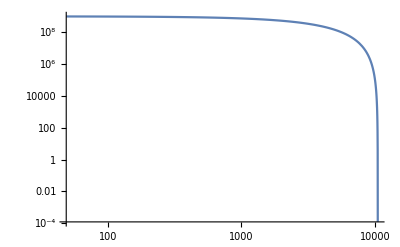

```mathematica
rho3[z_]= -0.0008704524348117549 (-1.1488278509052148*^12+3.2907222305990475*^8 z-31420.0042835725 z^2+1. z^3)
LogLogPlot[rho3[z],{z,0,50000}, PlotRange->All]
```

```mathematica
PacData=Flatten[Table[{path, Integrate[Evaluate[rho[z]/.sol],{z, 9313,path }]},{path, 0, 9313, 10}], 1]
```

{0,{-2.58846×10^12},10,{-2.57848×10^12},20,{-2.56852×10^12},30,{-2.55859×10^12},40,{-2.54869×10^12},50,{-2.53882×10^12},60,{-2.52898×10^12},70,{-2.51916×10^12},80,{-2.50938×10^12},90,{-2.49962×10^12},100,{-2.48989×10^12},110,{-2.48019×10^12},120,{-2.47052×10^12},130,{-2.46088×10^12},140,{-2.45126×10^12},150,{-2.44167×10^12},160,{-2.43211×10^12},170,{-2.42258×10^12},180,{-2.41308×10^12},190,{-2.4036×10^12},200,{-2.39415×10^12},210,{-2.38473×10^12},220,{-2.37534×10^12},230,{-2.36597×10^12},240,{-2.35663×10^12},250,{-2.34732×10^12},260,{-2.33804×10^12},270,{-2.32878×10^12},280,{-2.31955×10^12},290,{-2.31035×10^12},300,{-2.30118×10^12},310,{-2.29203×10^12},320,{-2.28291×10^12},330,{-2.27382×10^12},340,{-2.26475×10^12},350,{-2.25571×10^12},360,{-2.2467×10^12},370,{-2.23772×10^12},380,{-2.22876×10^12},390,{-2.21983×10^12},400,{-2.21092×10^12},410,{-2.20205×10^12},420,{-2.19319×10^12},430,{-2.18437×10^12},440,{-2.17557×10^12},450,{-2.1668×10^12},460,{-2.15805×10^12},470,{-2.14933×10^12},480,{-2.14064×10^12},490,{-2.13197×10^12},500,{-2.12333×10^12},510,{-2.11472×10^12},520,{-2.10613×10^12},530,{-2.09757×10^12},540,{-2.08903×10^12},550,{-2.08052×10^12},560,{-2.07204×10^12},570,{-2.06358×10^12},580,{-2.05515×10^12},590,{-2.04674×10^12},600,{-2.03836×10^12},610,{-2.03×10^12},620,{-2.02167×10^12},630,{-2.01336×10^12},640,{-2.00508×10^12},650,{-1.99683×10^12},660,{-1.9886×10^12},670,{-1.9804×10^12},680,{-1.97222×10^12},690,{-1.96407×10^12},700,{-1.95594×10^12},710,{-1.94784×10^12},720,{-1.93976×10^12},730,{-1.9317×10^12},740,{-1.92368×10^12},750,{-1.91567×10^12},760,{-1.90769×10^12},770,{-1.89974×10^12},780,{-1.89181×10^12},790,{-1.88391×10^12},800,{-1.87603×10^12},810,{-1.86817×10^12},820,{-1.86034×10^12},830,{-1.85254×10^12},840,{-1.84476×10^12},850,{-1.837×10^12},860,{-1.82927×10^12},870,{-1.82156×10^12},880,{-1.81387×10^12},890,{-1.80621×10^12},900,{-1.79858×10^12},910,{-1.79096×10^12},920,{-1.78338×10^12},930,{-1.77581×10^12},940,{-1.76827×10^12},950,{-1.76076×10^12},960,{-1.75326×10^12},970,{-1.7458×10^12},980,{-1.73835×10^12},990,{-1.73093×10^12},1000,{-1.72353×10^12},1010,{-1.71616×10^12},1020,{-1.70881×10^12},1030,{-1.70148×10^12},1040,{-1.69418×10^12},1050,{-1.6869×10^12},1060,{-1.67964×10^12},1070,{-1.6724×10^12},1080,{-1.66519×10^12},1090,{-1.65801×10^12},1100,{-1.65084×10^12},1110,{-1.6437×10^12},1120,{-1.63658×10^12},1130,{-1.62949×10^12},1140,{-1.62242×10^12},1150,{-1.61537×10^12},1160,{-1.60834×10^12},1170,{-1.60134×10^12},1180,{-1.59435×10^12},1190,{-1.5874×10^12},1200,{-1.58046×10^12},1210,{-1.57355×10^12},1220,{-1.56666×10^12},1230,{-1.55979×10^12},1240,{-1.55294×10^12},1250,{-1.54612×10^12},1260,{-1.53932×10^12},1270,{-1.53254×10^12},1280,{-1.52578×10^12},1290,{-1.51905×10^12},1300,{-1.51234×10^12},1310,{-1.50565×10^12},1320,{-1.49898×10^12},1330,{-1.49233×10^12},1340,{-1.48571×10^12},1350,{-1.47911×10^12},1360,{-1.47253×10^12},1370,{-1.46597×10^12},1380,{-1.45943×10^12},1390,{-1.45292×10^12},1400,{-1.44642×10^12},1410,{-1.43995×10^12},1420,{-1.4335×10^12},1430,{-1.42707×10^12},1440,{-1.42067×10^12},1450,{-1.41428×10^12},1460,{-1.40792×10^12},1470,{-1.40157×10^12},1480,{-1.39525×10^12},1490,{-1.38895×10^12},1500,{-1.38267×10^12},1510,{-1.37641×10^12},1520,{-1.37018×10^12},1530,{-1.36396×10^12},1540,{-1.35777×10^12},1550,{-1.35159×10^12},1560,{-1.34544×10^12},1570,{-1.33931×10^12},1580,{-1.3332×10^12},1590,{-1.3271×10^12},1600,{-1.32103×10^12},1610,{-1.31499×10^12},1620,{-1.30896×10^12},1630,{-1.30295×10^12},1640,{-1.29696×10^12},1650,{-1.29099×10^12},1660,{-1.28505×10^12},1670,{-1.27912×10^12},1680,{-1.27322×10^12},1690,{-1.26733×10^12},1700,{-1.26146×10^12},1710,{-1.25562×10^12},1720,{-1.24979×10^12},1730,{-1.24399×10^12},1740,{-1.23821×10^12},1750,{-1.23244×10^12},1760,{-1.2267×10^12},1770,{-1.22097×10^12},1780,{-1.21527×10^12},1790,{-1.20958×10^12},1800,{-1.20392×10^12},1810,{-1.19827×10^12},1820,{-1.19265×10^12},1830,{-1.18704×10^12},1840,{-1.18145×10^12},1850,{-1.17589×10^12},1860,{-1.17034×10^12},1870,{-1.16481×10^12},1880,{-1.1593×10^12},1890,{-1.15381×10^12},1900,{-1.14834×10^12},1910,{-1.14289×10^12},1920,{-1.13746×10^12},1930,{-1.13205×10^12},1940,{-1.12666×10^12},1950,{-1.12128×10^12},1960,{-1.11593×10^12},1970,{-1.11059×10^12},1980,{-1.10528×10^12},1990,{-1.09998×10^12},2000,{-1.0947×10^12},2010,{-1.08944×10^12},2020,{-1.0842×10^12},2030,{-1.07898×10^12},2040,{-1.07377×10^12},2050,{-1.06859×10^12},2060,{-1.06342×10^12},2070,{-1.05827×10^12},2080,{-1.05315×10^12},2090,{-1.04803×10^12},2100,{-1.04294×10^12},2110,{-1.03787×10^12},2120,{-1.03281×10^12},2130,{-1.02778×10^12},2140,{-1.02276×10^12},2150,{-1.01776×10^12},2160,{-1.01277×10^12},2170,{-1.00781×10^12},2180,{-1.00286×10^12},2190,{-9.97935×10^11},2200,{-9.93025×10^11},2210,{-9.88133×10^11},2220,{-9.83259×10^11},2230,{-9.78403×10^11},2240,{-9.73564×10^11},2250,{-9.68744×10^11},2260,{-9.63941×10^11},2270,{-9.59155×10^11},2280,{-9.54388×10^11},2290,{-9.49638×10^11},2300,{-9.44906×10^11},2310,{-9.40191×10^11},2320,{-9.35494×10^11},2330,{-9.30814×10^11},2340,{-9.26151×10^11},2350,{-9.21506×10^11},2360,{-9.16879×10^11},2370,{-9.12268×10^11},2380,{-9.07675×10^11},2390,{-9.03099×10^11},2400,{-8.9854×10^11},2410,{-8.93998×10^11},2420,{-8.89474×10^11},2430,{-8.84966×10^11},2440,{-8.80475×10^11},2450,{-8.76002×10^11},2460,{-8.71545×10^11},2470,{-8.67105×10^11},2480,{-8.62682×10^11},2490,{-8.58275×10^11},2500,{-8.53886×10^11},2510,{-8.49513×10^11},2520,{-8.45156×10^11},2530,{-8.40817×10^11},2540,{-8.36493×10^11},2550,{-8.32187×10^11},2560,{-8.27897×10^11},2570,{-8.23623×10^11},2580,{-8.19366×10^11},2590,{-8.15125×10^11},2600,{-8.109×10^11},2610,{-8.06692×10^11},2620,{-8.025×10^11},2630,{-7.98324×10^11},2640,{-7.94164×10^11},2650,{-7.9002×10^11},2660,{-7.85893×10^11},2670,{-7.81781×10^11},2680,{-7.77686×10^11},2690,{-7.73606×10^11},2700,{-7.69542×10^11},2710,{-7.65494×10^11},2720,{-7.61462×10^11},2730,{-7.57446×10^11},2740,{-7.53445×10^11},2750,{-7.49461×10^11},2760,{-7.45491×10^11},2770,{-7.41538×10^11},2780,{-7.376×10^11},2790,{-7.33677×10^11},2800,{-7.2977×10^11},2810,{-7.25879×10^11},2820,{-7.22003×10^11},2830,{-7.18142×10^11},2840,{-7.14297×10^11},2850,{-7.10467×10^11},2860,{-7.06652×10^11},2870,{-7.02852×10^11},2880,{-6.99068×10^11},2890,{-6.95299×10^11},2900,{-6.91544×10^11},2910,{-6.87805×10^11},2920,{-6.84081×10^11},2930,{-6.80372×10^11},2940,{-6.76678×10^11},2950,{-6.72998×10^11},2960,{-6.69334×10^11},2970,{-6.65684×10^11},2980,{-6.62049×10^11},2990,{-6.58429×10^11},3000,{-6.54824×10^11},3010,{-6.51233×10^11},3020,{-6.47657×10^11},3030,{-6.44095×10^11},3040,{-6.40548×10^11},3050,{-6.37016×10^11},3060,{-6.33498×10^11},3070,{-6.29994×10^11},3080,{-6.26505×10^11},3090,{-6.2303×10^11},3100,{-6.19569×10^11},3110,{-6.16123×10^11},3120,{-6.12691×10^11},3130,{-6.09273×10^11},3140,{-6.05869×10^11},3150,{-6.02479×10^11},3160,{-5.99104×10^11},3170,{-5.95742×10^11},3180,{-5.92395×10^11},3190,{-5.89061×10^11},3200,{-5.85741×10^11},3210,{-5.82435×10^11},3220,{-5.79143×10^11},3230,{-5.75865×10^11},3240,{-5.72601×10^11},3250,{-5.6935×10^11},3260,{-5.66113×10^11},3270,{-5.6289×10^11},3280,{-5.5968×10^11},3290,{-5.56484×10^11},3300,{-5.53302×10^11},3310,{-5.50133×10^11},3320,{-5.46977×10^11},3330,{-5.43835×10^11},3340,{-5.40706×10^11},3350,{-5.37591×10^11},3360,{-5.34489×10^11},3370,{-5.314×10^11},3380,{-5.28324×10^11},3390,{-5.25262×10^11},3400,{-5.22212×10^11},3410,{-5.19176×10^11},3420,{-5.16153×10^11},3430,{-5.13143×10^11},3440,{-5.10146×10^11},3450,{-5.07162×10^11},3460,{-5.04191×10^11},3470,{-5.01233×10^11},3480,{-4.98288×10^11},3490,{-4.95356×10^11},3500,{-4.92436×10^11},3510,{-4.89529×10^11},3520,{-4.86635×10^11},3530,{-4.83753×10^11},3540,{-4.80885×10^11},3550,{-4.78028×10^11},3560,{-4.75185×10^11},3570,{-4.72354×10^11},3580,{-4.69535×10^11},3590,{-4.66729×10^11},3600,{-4.63935×10^11},3610,{-4.61154×10^11},3620,{-4.58385×10^11},3630,{-4.55628×10^11},3640,{-4.52884×10^11},3650,{-4.50152×10^11},3660,{-4.47432×10^11},3670,{-4.44724×10^11},3680,{-4.42029×10^11},3690,{-4.39345×10^11},3700,{-4.36674×10^11},3710,{-4.34015×10^11},3720,{-4.31367×10^11},3730,{-4.28732×10^11},3740,{-4.26108×10^11},3750,{-4.23497×10^11},3760,{-4.20897×10^11},3770,{-4.18309×10^11},3780,{-4.15733×10^11},3790,{-4.13169×10^11},3800,{-4.10616×10^11},3810,{-4.08075×10^11},3820,{-4.05546×10^11},3830,{-4.03028×10^11},3840,{-4.00522×10^11},3850,{-3.98027×10^11},3860,{-3.95544×10^11},3870,{-3.93072×10^11},3880,{-3.90612×10^11},3890,{-3.88163×10^11},3900,{-3.85726×10^11},3910,{-3.833×10^11},3920,{-3.80885×10^11},3930,{-3.78482×10^11},3940,{-3.76089×10^11},3950,{-3.73708×10^11},3960,{-3.71338×10^11},3970,{-3.68979×10^11},3980,{-3.66632×10^11},3990,{-3.64295×10^11},4000,{-3.61969×10^11},4010,{-3.59654×10^11},4020,{-3.57351×10^11},4030,{-3.55058×10^11},4040,{-3.52776×10^11},4050,{-3.50505×10^11},4060,{-3.48245×10^11},4070,{-3.45995×10^11},4080,{-3.43756×10^11},4090,{-3.41528×10^11},4100,{-3.39311×10^11},4110,{-3.37104×10^11},4120,{-3.34908×10^11},4130,{-3.32723×10^11},4140,{-3.30548×10^11},4150,{-3.28383×10^11},4160,{-3.26229×10^11},4170,{-3.24086×10^11},4180,{-3.21953×10^11},4190,{-3.1983×10^11},4200,{-3.17718×10^11},4210,{-3.15616×10^11},4220,{-3.13524×10^11},4230,{-3.11442×10^11},4240,{-3.09371×10^11},4250,{-3.0731×10^11},4260,{-3.05259×10^11},4270,{-3.03218×10^11},4280,{-3.01187×10^11},4290,{-2.99167×10^11},4300,{-2.97156×10^11},4310,{-2.95155×10^11},4320,{-2.93164×10^11},4330,{-2.91184×10^11},4340,{-2.89213×10^11},4350,{-2.87251×10^11},4360,{-2.853×10^11},4370,{-2.83359×10^11},4380,{-2.81427×10^11},4390,{-2.79505×10^11},4400,{-2.77593×10^11},4410,{-2.7569×10^11},4420,{-2.73797×10^11},4430,{-2.71914×10^11},4440,{-2.7004×10^11},4450,{-2.68176×10^11},4460,{-2.66321×10^11},4470,{-2.64475×10^11},4480,{-2.6264×10^11},4490,{-2.60813×10^11},4500,{-2.58996×10^11},4510,{-2.57188×10^11},4520,{-2.5539×10^11},4530,{-2.53601×10^11},4540,{-2.51821×10^11},4550,{-2.5005×10^11},4560,{-2.48289×10^11},4570,{-2.46536×10^11},4580,{-2.44793×10^11},4590,{-2.43059×10^11},4600,{-2.41334×10^11},4610,{-2.39618×10^11},4620,{-2.37911×10^11},4630,{-2.36213×10^11},4640,{-2.34524×10^11},4650,{-2.32844×10^11},4660,{-2.31172×10^11},4670,{-2.2951×10^11},4680,{-2.27856×10^11},4690,{-2.26212×10^11},4700,{-2.24575×10^11},4710,{-2.22948×10^11},4720,{-2.21329×10^11},4730,{-2.19719×10^11},4740,{-2.18118×10^11},4750,{-2.16525×10^11},4760,{-2.14941×10^11},4770,{-2.13365×10^11},4780,{-2.11798×10^11},4790,{-2.1024×10^11},4800,{-2.08689×10^11},4810,{-2.07148×10^11},4820,{-2.05614×10^11},4830,{-2.04089×10^11},4840,{-2.02573×10^11},4850,{-2.01064×10^11},4860,{-1.99564×10^11},4870,{-1.98072×10^11},4880,{-1.96589×10^11},4890,{-1.95113×10^11},4900,{-1.93646×10^11},4910,{-1.92187×10^11},4920,{-1.90736×10^11},4930,{-1.89293×10^11},4940,{-1.87858×10^11},4950,{-1.86431×10^11},4960,{-1.85012×10^11},4970,{-1.83601×10^11},4980,{-1.82198×10^11},4990,{-1.80803×10^11},5000,{-1.79415×10^11},5010,{-1.78036×10^11},5020,{-1.76664×10^11},5030,{-1.753×10^11},5040,{-1.73944×10^11},5050,{-1.72596×10^11},5060,{-1.71255×10^11},5070,{-1.69922×10^11},5080,{-1.68596×10^11},5090,{-1.67278×10^11},5100,{-1.65968×10^11},5110,{-1.64666×10^11},5120,{-1.6337×10^11},5130,{-1.62083×10^11},5140,{-1.60802×10^11},5150,{-1.5953×10^11},5160,{-1.58264×10^11},5170,{-1.57006×10^11},5180,{-1.55756×10^11},5190,{-1.54512×10^11},5200,{-1.53276×10^11},5210,{-1.52047×10^11},5220,{-1.50826×10^11},5230,{-1.49612×10^11},5240,{-1.48404×10^11},5250,{-1.47204×10^11},5260,{-1.46012×10^11},5270,{-1.44826×10^11},5280,{-1.43647×10^11},5290,{-1.42475×10^11},5300,{-1.41311×10^11},5310,{-1.40153×10^11},5320,{-1.39003×10^11},5330,{-1.37859×10^11},5340,{-1.36722×10^11},5350,{-1.35592×10^11},5360,{-1.34469×10^11},5370,{-1.33353×10^11},5380,{-1.32243×10^11},5390,{-1.31141×10^11},5400,{-1.30045×10^11},5410,{-1.28956×10^11},5420,{-1.27873×10^11},5430,{-1.26797×10^11},5440,{-1.25728×10^11},5450,{-1.24666×10^11},5460,{-1.2361×10^11},5470,{-1.2256×10^11},5480,{-1.21517×10^11},5490,{-1.20481×10^11},5500,{-1.19451×10^11},5510,{-1.18428×10^11},5520,{-1.17411×10^11},5530,{-1.164×10^11},5540,{-1.15396×10^11},5550,{-1.14398×10^11},5560,{-1.13406×10^11},5570,{-1.12421×10^11},5580,{-1.11442×10^11},5590,{-1.10469×10^11},5600,{-1.09503×10^11},5610,{-1.08543×10^11},5620,{-1.07588×10^11},5630,{-1.0664×10^11},5640,{-1.05698×10^11},5650,{-1.04763×10^11},5660,{-1.03833×10^11},5670,{-1.02909×10^11},5680,{-1.01992×10^11},5690,{-1.0108×10^11},5700,{-1.00174×10^11},5710,{-9.92745×10^10},5720,{-9.83806×10^10},5730,{-9.74926×10^10},5740,{-9.66105×10^10},5750,{-9.57343×10^10},5760,{-9.48638×10^10},5770,{-9.39991×10^10},5780,{-9.31403×10^10},5790,{-9.22871×10^10},5800,{-9.14397×10^10},5810,{-9.05979×10^10},5820,{-8.97618×10^10},5830,{-8.89314×10^10},5840,{-8.81065×10^10},5850,{-8.72873×10^10},5860,{-8.64736×10^10},5870,{-8.56655×10^10},5880,{-8.48629×10^10},5890,{-8.40658×10^10},5900,{-8.32741×10^10},5910,{-8.24879×10^10},5920,{-8.17072×10^10},5930,{-8.09318×10^10},5940,{-8.01618×10^10},5950,{-7.93971×10^10},5960,{-7.86378×10^10},5970,{-7.78837×10^10},5980,{-7.7135×10^10},5990,{-7.63915×10^10},6000,{-7.56532×10^10},6010,{-7.49201×10^10},6020,{-7.41923×10^10},6030,{-7.34695×10^10},6040,{-7.27519×10^10},6050,{-7.20395×10^10},6060,{-7.13321×10^10},6070,{-7.06297×10^10},6080,{-6.99325×10^10},6090,{-6.92402×10^10},6100,{-6.85529×10^10},6110,{-6.78706×10^10},6120,{-6.71933×10^10},6130,{-6.65208×10^10},6140,{-6.58533×10^10},6150,{-6.51907×10^10},6160,{-6.45329×10^10},6170,{-6.38799×10^10},6180,{-6.32318×10^10},6190,{-6.25884×10^10},6200,{-6.19498×10^10},6210,{-6.1316×10^10},6220,{-6.06868×10^10},6230,{-6.00624×10^10},6240,{-5.94426×10^10},6250,{-5.88275×10^10},6260,{-5.82171×10^10},6270,{-5.76112×10^10},6280,{-5.70099×10^10},6290,{-5.64132×10^10},6300,{-5.5821×10^10},6310,{-5.52333×10^10},6320,{-5.46502×10^10},6330,{-5.40715×10^10},6340,{-5.34972×10^10},6350,{-5.29274×10^10},6360,{-5.2362×10^10},6370,{-5.1801×10^10},6380,{-5.12443×10^10},6390,{-5.0692×10^10},6400,{-5.01441×10^10},6410,{-4.96004×10^10},6420,{-4.9061×10^10},6430,{-4.85258×10^10},6440,{-4.79949×10^10},6450,{-4.74682×10^10},6460,{-4.69457×10^10},6470,{-4.64273×10^10},6480,{-4.59131×10^10},6490,{-4.54031×10^10},6500,{-4.48971×10^10},6510,{-4.43953×10^10},6520,{-4.38975×10^10},6530,{-4.34037×10^10},6540,{-4.2914×10^10},6550,{-4.24282×10^10},6560,{-4.19465×10^10},6570,{-4.14687×10^10},6580,{-4.09948×10^10},6590,{-4.05249×10^10},6600,{-4.00589×10^10},6610,{-3.95967×10^10},6620,{-3.91384×10^10},6630,{-3.86839×10^10},6640,{-3.82333×10^10},6650,{-3.77864×10^10},6660,{-3.73434×10^10},6670,{-3.69041×10^10},6680,{-3.64685×10^10},6690,{-3.60366×10^10},6700,{-3.56084×10^10},6710,{-3.51839×10^10},6720,{-3.47631×10^10},6730,{-3.43459×10^10},6740,{-3.39323×10^10},6750,{-3.35223×10^10},6760,{-3.31158×10^10},6770,{-3.2713×10^10},6780,{-3.23136×10^10},6790,{-3.19178×10^10},6800,{-3.15255×10^10},6810,{-3.11366×10^10},6820,{-3.07513×10^10},6830,{-3.03693×10^10},6840,{-2.99908×10^10},6850,{-2.96156×10^10},6860,{-2.92439×10^10},6870,{-2.88755×10^10},6880,{-2.85104×10^10},6890,{-2.81487×10^10},6900,{-2.77903×10^10},6910,{-2.74351×10^10},6920,{-2.70833×10^10},6930,{-2.67346×10^10},6940,{-2.63892×10^10},6950,{-2.6047×10^10},6960,{-2.5708×10^10},6970,{-2.53722×10^10},6980,{-2.50395×10^10},6990,{-2.47099×10^10},7000,{-2.43835×10^10},7010,{-2.40602×10^10},7020,{-2.37399×10^10},7030,{-2.34227×10^10},7040,{-2.31085×10^10},7050,{-2.27974×10^10},7060,{-2.24893×10^10},7070,{-2.21841×10^10},7080,{-2.18819×10^10},7090,{-2.15827×10^10},7100,{-2.12864×10^10},7110,{-2.0993×10^10},7120,{-2.07025×10^10},7130,{-2.04149×10^10},7140,{-2.01302×10^10},7150,{-1.98483×10^10},7160,{-1.95692×10^10},7170,{-1.92929×10^10},7180,{-1.90194×10^10},7190,{-1.87487×10^10},7200,{-1.84807×10^10},7210,{-1.82155×10^10},7220,{-1.7953×10^10},7230,{-1.76932×10^10},7240,{-1.74361×10^10},7250,{-1.71816×10^10},7260,{-1.69298×10^10},7270,{-1.66807×10^10},7280,{-1.64341×10^10},7290,{-1.61902×10^10},7300,{-1.59488×10^10},7310,{-1.571×10^10},7320,{-1.54737×10^10},7330,{-1.524×10^10},7340,{-1.50088×10^10},7350,{-1.47801×10^10},7360,{-1.45538×10^10},7370,{-1.43301×10^10},7380,{-1.41087×10^10},7390,{-1.38898×10^10},7400,{-1.36734×10^10},7410,{-1.34593×10^10},7420,{-1.32476×10^10},7430,{-1.30383×10^10},7440,{-1.28313×10^10},7450,{-1.26266×10^10},7460,{-1.24243×10^10},7470,{-1.22242×10^10},7480,{-1.20265×10^10},7490,{-1.1831×10^10},7500,{-1.16378×10^10},7510,{-1.14468×10^10},7520,{-1.1258×10^10},7530,{-1.10714×10^10},7540,{-1.0887×10^10},7550,{-1.07048×10^10},7560,{-1.05248×10^10},7570,{-1.03469×10^10},7580,{-1.01711×10^10},7590,{-9.9974×10^9},7600,{-9.82582×10^9},7610,{-9.65632×10^9},7620,{-9.48889×10^9},7630,{-9.3235×10^9},7640,{-9.16014×10^9},7650,{-8.99881×10^9},7660,{-8.83947×10^9},7670,{-8.68213×10^9},7680,{-8.52676×10^9},7690,{-8.37334×10^9},7700,{-8.22187×10^9},7710,{-8.07233×10^9},7720,{-7.9247×10^9},7730,{-7.77896×10^9},7740,{-7.63512×10^9},7750,{-7.49314×10^9},7760,{-7.35301×10^9},7770,{-7.21473×10^9},7780,{-7.07827×10^9},7790,{-6.94362×10^9},7800,{-6.81076×10^9},7810,{-6.67969×10^9},7820,{-6.55039×10^9},7830,{-6.42283×10^9},7840,{-6.29702×10^9},7850,{-6.17293×10^9},7860,{-6.05056×10^9},7870,{-5.92987×10^9},7880,{-5.81088×10^9},7890,{-5.69354×10^9},7900,{-5.57787×10^9},7910,{-5.46383×10^9},7920,{-5.35142×10^9},7930,{-5.24063×10^9},7940,{-5.13143×10^9},7950,{-5.02382×10^9},7960,{-4.91777×10^9},7970,{-4.81329×10^9},7980,{-4.71035×10^9},7990,{-4.60895×10^9},8000,{-4.50906×10^9},8010,{-4.41067×10^9},8020,{-4.31378×10^9},8030,{-4.21836×10^9},8040,{-4.12441×10^9},8050,{-4.03191×10^9},8060,{-3.94084×10^9},8070,{-3.85121×10^9},8080,{-3.76298×10^9},8090,{-3.67615×10^9},8100,{-3.59071×10^9},8110,{-3.50664×10^9},8120,{-3.42393×10^9},8130,{-3.34257×10^9},8140,{-3.26254×10^9},8150,{-3.18384×10^9},8160,{-3.10644×10^9},8170,{-3.03035×10^9},8180,{-2.95553×10^9},8190,{-2.88199×10^9},8200,{-2.8097×10^9},8210,{-2.73867×10^9},8220,{-2.66886×10^9},8230,{-2.60028×10^9},8240,{-2.53291×10^9},8250,{-2.46674×10^9},8260,{-2.40175×10^9},8270,{-2.33794×10^9},8280,{-2.27529×10^9},8290,{-2.21379×10^9},8300,{-2.15342×10^9},8310,{-2.09418×10^9},8320,{-2.03605×10^9},8330,{-1.97903×10^9},8340,{-1.92309×10^9},8350,{-1.86824×10^9},8360,{-1.81445×10^9},8370,{-1.76171×10^9},8380,{-1.71002×10^9},8390,{-1.65936×10^9},8400,{-1.60972×10^9},8410,{-1.56109×10^9},8420,{-1.51346×10^9},8430,{-1.46681×10^9},8440,{-1.42114×10^9},8450,{-1.37643×10^9},8460,{-1.33268×10^9},8470,{-1.28987×10^9},8480,{-1.24798×10^9},8490,{-1.20702×10^9},8500,{-1.16696×10^9},8510,{-1.1278×10^9},8520,{-1.08953×10^9},8530,{-1.05213×10^9},8540,{-1.0156×10^9},8550,{-9.7992×10^8},8560,{-9.45084×10^8},8570,{-9.1108×10^8},8580,{-8.77897×10^8},8590,{-8.45526×10^8},8600,{-8.13955×10^8},8610,{-7.83174×10^8},8620,{-7.53173×10^8},8630,{-7.2394×10^8},8640,{-6.95466×10^8},8650,{-6.6774×10^8},8660,{-6.40752×10^8},8670,{-6.14492×10^8},8680,{-5.88949×10^8},8690,{-5.64113×10^8},8700,{-5.39975×10^8},8710,{-5.16523×10^8},8720,{-4.93748×10^8},8730,{-4.7164×10^8},8740,{-4.50188×10^8},8750,{-4.29384×10^8},8760,{-4.09216×10^8},8770,{-3.89675×10^8},8780,{-3.70752×10^8},8790,{-3.52435×10^8},8800,{-3.34717×10^8},8810,{-3.17586×10^8},8820,{-3.01033×10^8},8830,{-2.85049×10^8},8840,{-2.69624×10^8},8850,{-2.54747×10^8},8860,{-2.4041×10^8},8870,{-2.26603×10^8},8880,{-2.13317×10^8},8890,{-2.00542×10^8},8900,{-1.88268×10^8},8910,{-1.76486×10^8},8920,{-1.65186×10^8},8930,{-1.5436×10^8},8940,{-1.43998×10^8},8950,{-1.3409×10^8},8960,{-1.24626×10^8},8970,{-1.15599×10^8},8980,{-1.06998×10^8},8990,{-9.88141×10^7},9000,{-9.10378×10^7},9010,{-8.36599×10^7},9020,{-7.66711×10^7},9030,{-7.00621×10^7},9040,{-6.38236×10^7},9050,{-5.79462×10^7},9060,{-5.24207×10^7},9070,{-4.72376×10^7},9080,{-4.23876×10^7},9090,{-3.78612×10^7},9100,{-3.36492×10^7},9110,{-2.97419×10^7},9120,{-2.61298×10^7},9130,{-2.28035×10^7},9140,{-1.97531×10^7},9150,{-1.69691×10^7},9160,{-1.44415×10^7},9170,{-1.21605×10^7},9180,{-1.01159×10^7},9190,{-8.29766×10^6},9200,{-6.69528×10^6},9210,{-5.29819×10^6},9220,{-4.09557×10^6},9230,{-3.07628×10^6},9240,{-2.22881×10^6},9250,{-1.54124×10^6},9260,{-1.00105×10^6},9270,{-595003.},9280,{-308895.},9290,{-127107.},9300,{-31833.},9310,{-1112.63}}

```mathematica
Export["Paczynski_column.csv",PacData,"CSV"]
```

Paczynski_column.csv

```mathematica
Integrate[Evaluate[rho[z]/.sol],{z, 9313, 0}]
```

{-2.58846×10^12}

```mathematica
combined = Piecewise[{{rho2[z], z<8805.68},{rho3[z], z≥8805.68}}]
```

Piecewise[{{117.161 (9864.57-1. z)^(3/2), z<8805.68}, {-0.000870452 (-1.14883×10^12+3.29072×10^8 z-31420. z^2+1. z^3), z≥8805.68}, {0, True}}]

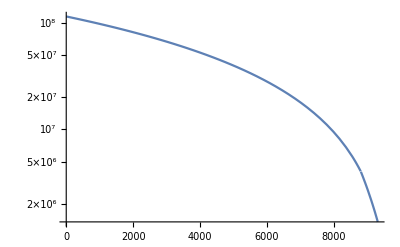

```mathematica
LogPlot[combined, {z, 0, 9313}]
```

```mathematica
combinedData = Table[zi, Integrate[combined, {z, 9313, zi}], {zi, 0, 9313, 1000}]
```

Integrate::pwrl: Unable to prove that integration limits {9313,zi} are real. Adding assumptions may help.

Table::nliter: Non-list iterator ∫_9313^zi combinedⅆz at position 2 does not evaluate to a real numeric value.

Table[zi,∫_9313^zi combinedⅆz,{zi,0,9313,1000}]

```mathematica
Integrate[combined, {z, 9313, 9313}]
```

0

```mathematica
NRData =  Table[path, Integrate[rho3[z], {z, 9313, path}], {path, 8808.68,  9313, 1}]
```

Table::nliter: Non-list iterator ∫_9313^path rho3[z]ⅆz at position 2 does not evaluate to a real numeric value.

```mathematica
Table[path,∫_9313^path rho3[z]ⅆz,{path,8809,9312,1}]
```

Table::nliter: Non-list iterator ∫_9313^path rho3[z]ⅆz at position 2 does not evaluate to a real numeric value.

Table[path,∫_9313^path rho3[z]ⅆz,{path,8809,9312,1}]

```mathematica
Integrate[rho3[z], {z, 9313, 8808.68}]
```

-1.27655×10^9

```mathematica
Solve[rho3[z]==0, z]
```

{{z→10473.3},{z→10473.3},{z→10473.3}}